# Agile Journal Article: Structural Quality Drift in Agile Development

## A model for how software quality drifts from one iteration to another

```mathematica
Directory[]
```

/Users/jsubapple

```mathematica
(* Model Parameters *)
(* Probabilities of quality becoming better, worse, or staying the same *)
better = 0.2;
worse = 0.6;
same = 0.2;
```

```mathematica
(* Threshold quality score -- quality must not be lower than this score *)
qualityScoreThreshold = 3.0;
maxQualityScore = 4.0;
minQualityScore = 0;
```

```mathematica
startingQualityScore = maxQualityScore;
```

```mathematica
(* Step by which quality changes in each iteration *)
step = 0.5;
```

```mathematica
(* Random Walk Model *)
```

```mathematica
randomWalk[iterations_,options___]:= Module[{drift, 
qualitySteps,
qualityChange,
qualityDrift,
qualityPlot,
thresholdPlot
}, 
drift = RandomChoice[{better, worse, same} -> {step, -step, 0}, iterations];
qualitySteps = Accumulate[Join[{startingQualityScore},drift]];
(* If quality score > maxQualityScore set it back to maxQualityScore *)  
qualityChange = qualitySteps /. (x_ /; x> maxQualityScore) -> maxQualityScore;
(* If quality score < minQualityScore set it back to minQualityScore *)
qualityDrift = qualityChange /. (x_ /; x < minQualityScore) -> minQualityScore;
qualityPlot = ListLinePlot[{Range[0, iterations], qualityDrift}ᵀ, options];
thresholdPlot = ListLinePlot[{Range[0, iterations], Table[qualityScoreThreshold, {i, 0, iterations}]}ᵀ, ColorFunction -> "BrightBands"];
Show[qualityPlot, thresholdPlot]
];
```

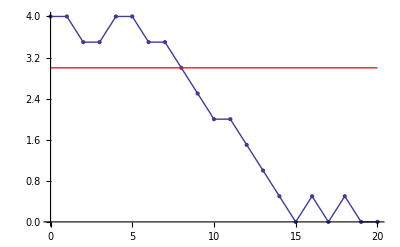
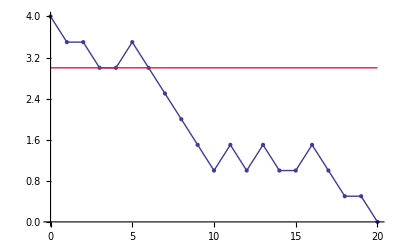
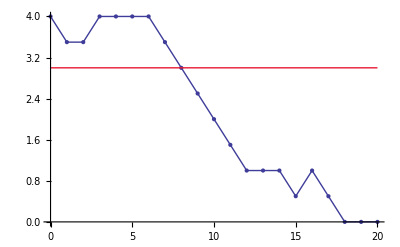
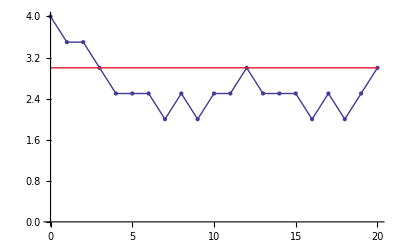
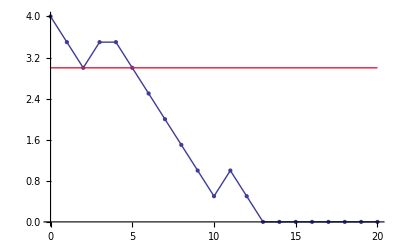
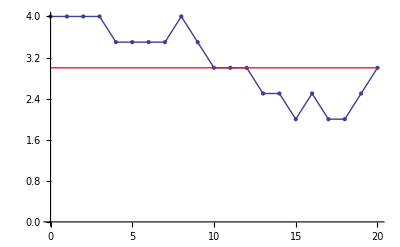
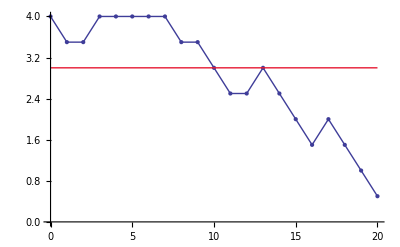
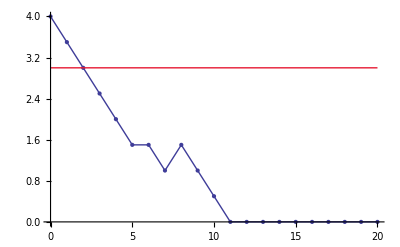

```mathematica
Table[randomWalk[20, Mesh -> All, PlotRange->{Automatic, {0,4}}], {20}]
```

```mathematica
qualityRandomWalk[nIterations_, pBetter_, pWorse_, pSame_, driftStepSize_] := Module[{qualityDrift, qualityDriftClean},
qualityDrift = NestList[# + RandomChoice[{pBetter, pWorse, pSame} -> {driftStepSize, -driftStepSize, 0}] &, maxQualityScore, nIterations];
(* Reset score to max or min if drift exceeds max or dips below min quality values *)
qualityDriftClean = qualityDrift/. (x_ /; x> maxQualityScore) -> maxQualityScore /. (x_ /; x < minQualityScore) -> minQualityScore
];
```

```mathematica
qualityRandomWalk[12, 0.2, 0.6, 0.2, 0.25]
```

{4.,4.,3.75,3.75,3.75,3.5,3.25,3.,2.75,2.5,2.5,2.25,2.25}

```mathematica
qualityDriftTrials[nTrials_, nIterations_, pBetter_, pWorse_, pSame_, driftStepSize_] := Module[{}, 
Table[qualityRandomWalk[nIterations, pBetter, pWorse, pSame, driftStepSize], {nTrials}]
];
```

```mathematica
trials = qualityDriftTrials[1000, 24, 0.2, 0.6, 0.2, 0.3];
```

```mathematica
avgQualityPerIteration = Thread[Mean[trials]]
```

{4.,3.8164,3.7069,3.5794,3.46,3.3505,3.2305,3.1153,3.0052,2.8915,2.7733,2.653,2.521,2.4049,2.2995,2.1816,2.0719,1.9659,1.8602,1.7461,1.6402,1.5248,1.4291,1.3331,1.2378}

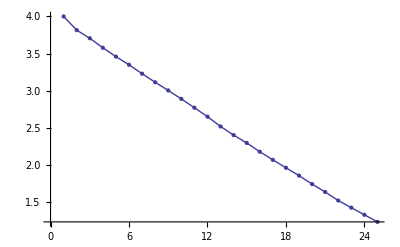

```mathematica
ListLinePlot[avgQualityPerIteration, Mesh->All]
```

```mathematica
plotAvgQualityPerIteration[nTrials_, nIterations_, pBetter_, pWorse_, pSame_,driftStepSize_, qualityThreshold_, options___] := Module[{trials,
avgQualityPerIteration,
thresholdPlotValues,
xAxisValues,
qualityDriftPlot,
thresholdPlot},
trials = qualityDriftTrials[nTrials, nIterations, pBetter, pWorse, pSame, driftStepSize];
avgQualityPerIteration = Thread[Mean[trials]];
thresholdPlotValues = Table[qualityThreshold, {i, 0, nIterations}];
xAxisValues = Range[0, nIterations];
(* {xAxisValues, thresholdPlotValues}ᵀ *)
qualityDriftPlot = ListLinePlot[{xAxisValues, avgQualityPerIteration}ᵀ, options];
thresholdPlot = ListLinePlot[thresholdPlotValues, ColorFunction -> "BrightBands", AxesOrigin->{0,0}];
Show[qualityDriftPlot, thresholdPlot]
];
```

```mathematica
Table[3.4, {12}]
```

{3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4}

```mathematica
{3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4}
```

{3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4,3.4}

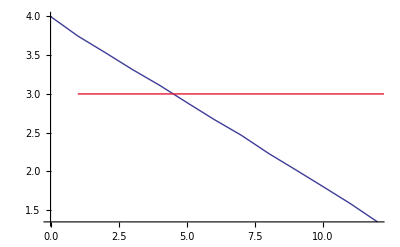

```mathematica
plotAvgQualityPerIteration[100, 12, 0.1, 0.8, 0.1, 0.3, 3.0]
```

```mathematica
plotOptions = {Mesh -> All, 
AxesOrigin -> {0,0},
Frame -> {True,True, False, False}, 
FrameLabel -> {"Iterations", "Structural Quality Score"},
BaseStyle->{Medium, FontFamily->"Arial",Bold},
LabelStyle->Directive[Black],
PlotRange->{Automatic, {0,4}}, 
FrameTicks->{Range[0,24], Range[0,4,0.5]}, 
AspectRatio -> 0.4, 
ImageSize -> 800};
```

```mathematica
(* Quality Drift Step Size Varies from 0.1 to 0.5 *)
(* High Complexity Scenario *)
(* pBetter = 0.1, pWorse = 0.8 pSame = 0.1 *)
```

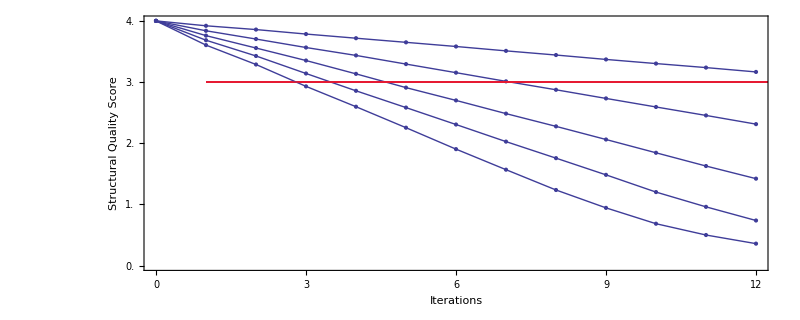

```mathematica
hiComplexity = Show[plotAvgQualityPerIteration[1000, 12, 0.1, 0.8, 0.1, #, 3.0, plotOptions] & /@ {0.1, 0.2, 0.3, 0.4, 0.5}]
```

```mathematica
(* Quality Drift Step Size Varies from 0.1 to 0.5 *)
(* Medium Complexity Scenario *)
(* pBetter = 0.2, pWorse = 0.6, pSame = 0.2 *)
```

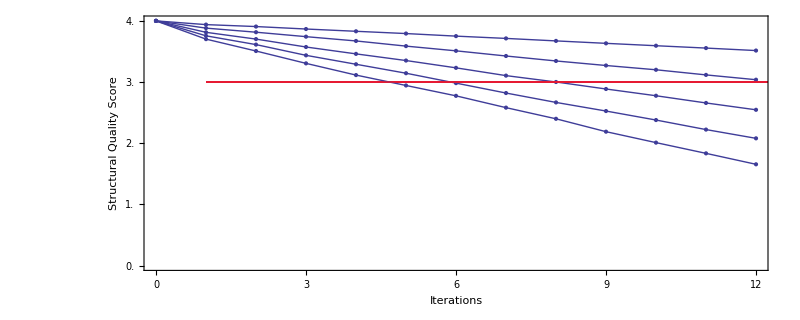

```mathematica
medComplexity = Show[plotAvgQualityPerIteration[1000, 12, 0.2, 0.6, 0.2, #, 3.0, plotOptions] & /@ {0.1, 0.2, 0.3, 0.4, 0.5}]
```

```mathematica
Export["AgileMediumComplexityQualityDrift.tif", medComplexity];
```

```mathematica
(* Quality Drift Step Size Varies from 0.1 to 0.5 *)
(* Low Complexity Scenario *)
(* pBetter = 0.3, pWorse = 0.4, pSame = 0.3 *)
```

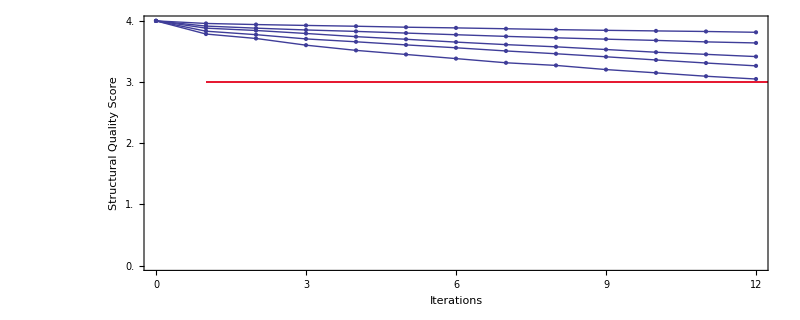

```mathematica
loComplexity = Show[plotAvgQualityPerIteration[1000, 12, 0.3, 0.4, 0.3, #, 3.0, plotOptions] & /@ {0.1, 0.2, 0.3, 0.4, 0.5}]
```

```mathematica
Export["AgileLowComplexityQualityDrift.tif", loComplexity];
```

```mathematica
qualityChage = Manipulate[Show[plotAvgQualityPerIteration[experiments,iterations, pBetter, pWorse, 0.1, #, threshold, plotOptions] & /@ {0.1, 0.2, 0.3, 0.4, 0.5}], {{experiments, 100, "Trials"}, {1, 10, 100, 1000}, Appearance->"Labeled"}, {iterations, {12, 24}}, {threshold, {2, 2.5, 3, 3.5}},{pBetter, 0.1, 1, 0.1}, {pWorse, 0.1, 1, 0.1}]
```

Show::gcomb: Could not combine the graphics objects in Show[«1»].